```mathematica
wave=Import["waveform_exercise.csv"];
```

```mathematica
ft=Fourier[wave[[;;,2]]];
```

```mathematica
data=Transpose[{Table[i,{i,0,999}],Abs[ft[[1;;1000]]]}];
```

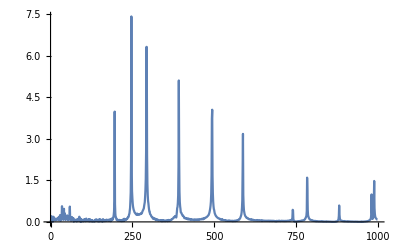

```mathematica
ListPlot[data,PlotRange->All,Joined->True]
```